```mathematica
Pane[Grid[{
{Style["Simulation of HD GDA thermodynamics","Title"]},{Style["Host/Dye 1:1 complex in a competitive guest displacement assay","Subtitle"]},
{MouseAppearance[Button[Style["Launch Application","Section"],{ nb=EvaluationNotebook[],NotebookFind[nb,"launchcell",All,CellTags],SelectionEvaluate[nb]},Appearance->None],"LinkHand"]}

}, Alignment->Center,ItemSize->Large,BaselinePosition->Baseline],Alignment->Center,ImageSize->Full]
```

Simulation of HD GDA thermodynamics
Host/Dye 1:1 complex in a competitive guest displacement assay
Launch Application

```mathematica
(* Notebook settings
*)
SetOptions[EvaluationNotebook[],CellContext->Notebook];
SetOptions[$FrontEnd,"DynamicUpdating"->True];
SetOptions[$FrontEnd,"DynamicEvaluationTimeout"->30];

(* Load Packges
*)	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","thermoHD-Comp","thermoCacheHD-1Comp1.0.0.4.m"}]}]];
	Get[FileNameJoin[{FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Packages","datagen.m"}]}]];
(* Paths
*)
tempPath=FileNameJoin[{NotebookDirectory[],"Parameter","temp-thermoHD-ADA1.mx"}];
defaultPath=FileNameJoin[{NotebookDirectory[],"Parameter","default-thermoHD-ADA1.mx"}];

initialparameters=Import[defaultPath];
	h0in=initialparameters[[1]];
	d0in=initialparameters[[2]];
	step=initialparameters[[3]];
	kequhdin=initialparameters[[4]];
	sig0in=initialparameters[[5]];
	sigdin=initialparameters[[6]];
	sighdin=initialparameters[[7]];
	ga0in=initialparameters[[8]];
	kequhgain=initialparameters[[9]];

(*Buttons
*)simulationbutton=MouseAppearance[Button["Simulate",{ nb=EvaluationNotebook[],NotebookFind[nb,"simroutineHG",All,CellTags],SelectionEvaluate[nb]},BaseStyle->EdgeForm[Dotted]],"LinkHand"];
variablessavebutton=MouseAppearance[Button["Save Parameters",{
initialparameters={
h0in,
d0in,
step,
kequhdin,
sig0in,
sigdin,
sighdin,
ga0in,
kequhgain
},Export[tempPath,initialparameters]},Appearance->"DialogBox"],"LinkHand"];
variablesloadbutton=MouseAppearance[Button["Load Saved Parameters",{
initialparameters=Import[tempPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

defaultloadbutton=MouseAppearance[Button["Load Default Parameters",{
initialparameters=Import[defaultPath],
	h0in=initialparameters[[1]],
	d0in=initialparameters[[2]],
	step=initialparameters[[3]],
	kequhdin=initialparameters[[4]],
	sig0in=initialparameters[[5]],
	sigdin=initialparameters[[6]],
	sighdin=initialparameters[[7]],
	ga0in=initialparameters[[8]],
	kequhgain=initialparameters[[9]]
	},Appearance->"DialogBox"],"LinkHand"];

inputline = {
   {
   Style["species", Bold,Underlined, FontSize->12 ,TextAlignment->Right], 
   Style["concentration", Bold,Underlined, FontSize->12 ,TextAlignment->Right],"",
   Style["binding", Bold,Underlined, FontSize->12 ,TextAlignment->Right]},

   {
   Style["Host:", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[h0in], FieldSize -> 6],"M",
Style["c-step ", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[step], FieldSize -> 6],"M"},
 {"",Dynamic[h0in*1000000],"μM","c-step","","",""},
 
 {Style["Dye:", Bold, FontSize->16 ,TextAlignment->Right], 
   InputField[Dynamic[d0in], FieldSize -> 6],"M",Style["K_equ(HD)" , Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[kequhdin], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[d0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhdin]],""},
 
 
 
   {Style["Guest:", Bold, FontSize->16 ,TextAlignment->Right], 
      InputField[Dynamic[ga0in], FieldSize -> 6],"M",Style["K_equ(HG)" , Bold, FontSize->16 ,TextAlignment->Right],
      InputField[Dynamic[kequhgain], FieldSize -> 6],"\!\(\*SuperscriptBox[\(M\), \(-1\)]\)"
},
   {"",Dynamic[ga0in*1000000],"μM","lg(K_equ)",Dynamic[Log10[kequhgain]],""},
   
   
   {Style["Signal-HD", Bold, FontSize->16 ,TextAlignment->Right], InputField[Dynamic[sighdin], FieldSize -> 6],"",
   
   Style["Signal-D", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sigdin], FieldSize -> 6],"",
   Style["Signal-0", Bold, FontSize->16 ,TextAlignment->Right],InputField[Dynamic[sig0in], FieldSize -> 6]},
      {"HD complex","","","dye alone","","","Startsignal"}  
    
};

Print[TableForm[{{simulationbutton,variablesloadbutton,variablessavebutton,defaultloadbutton}}]];

Print[TableForm[inputline, TableAlignments -> Left]];
Print[Style["IDA - ",Bold],Style["Indicator Displacement Assay ",Italic,Bold,FontColor->Gray],Style["ADA - ",Bold],Style["Analyte Displacement Assay ",Italic,Bold,FontColor->Gray],Style["SAIBA - ",Bold],Style["Simultaneous Analyte and Indicator Binding Assay ",Italic,Bold,FontColor->Gray]];
```

Simulate | Load Saved Parameters | Save Parameters | Load Default Parameters

species | concentration |  | binding |  |  |  | 
Host: |  | M | c-step  |  | M |  | 
 |  | μM | c-step |  |  |  | 
Dye: |  | M | K_equ(HD) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Guest: |  | M | K_equ(HG) |  | M^-1 |  | 
 |  | μM | lg(K_equ) |  |  |  | 
Signal-HD |  |  | Signal-D |  |  | Signal-0 | 
HD complex |  |  | dye alone |  |  | Startsignal |

IDA - Indicator Displacement Assay ADA - Analyte Displacement Assay SAIBA - Simultaneous Analyte and Indicator Binding Assay

```mathematica
mode="Ga0 varied";
datasignal=sthdADAcacheSignalData[kequhdin,kequhgain,h0in,d0in,ga0in,sig0in,sighdin,sigdin,step];
dataHD=sthdADAcacheHDData[kequhdin,kequhgain,h0in,d0in,ga0in,step];
dataD=sthdADAcacheDData[kequhdin,kequhgain,h0in,d0in,ga0in,step];



inputs={{"Quantity","Value"},
{"Mode",mode},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(HD2)",kequhdin},
{"conc(G)",ga0in},
{"Kequ(HG)",kequhgain},
{"Signal-0",sig0in},
{"Signal-HD",sighdin},
{"Signal-Dye",sigdin},
{"c-step",step}
};
header={"conc","Signal"};
units={"M","INT"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];

(*signaloutput=Join[datasignal,List/@datathermohd[[All,2]],List/@datathermohdd[[All,2]],List/@datathermohga[[All,2]],List/@datathermod[[All,2]],List/@datathermoga[[All,2]],List/@datathermoh[[All,2]],2];*)

signaloutput=datasignal;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];


Quiet[exportbutton2=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];
simplot2=Manipulate[Show[ListLinePlot[{a1*datasignal,a2*dataHD,a3*dataD},PlotRange->All,PlotLegends->{"Signal","[HD]","[D]","[HG_A]","[G_A]","[H]"},GridLines->{{h0in},{}}],ImageSize-> Large,AxesOrigin->{0,0},PlotLabel-> "Simulated Data"],{{a1,1,"Signal"},{1,0}},{{a2,0,"[HD]"},{1,0}},{{a3,0,"[D]"},{1,0}},ControlPlacement->Right];

Print[simplot2,TableForm[{"You can save simulated data:",exportbutton2}]];

Off[Export::chtype];
```

You can save simulated data:
Save-Sim

{{0.,9.00844×10^-17},{4.9×10^-8,4.40546×10^-9},{9.8×10^-8,8.79365×10^-9},{1.47×10^-7,1.31647×10^-8},{1.96×10^-7,1.75188×10^-8},{2.45×10^-7,2.18561×10^-8},{2.94×10^-7,2.61767×10^-8},{3.43×10^-7,3.04807×10^-8},{3.92×10^-7,3.47683×10^-8},{4.41×10^-7,3.90396×10^-8},{4.9×10^-7,4.32948×10^-8},{5.39×10^-7,4.75339×10^-8},{5.88×10^-7,5.17572×10^-8},{6.37×10^-7,5.59647×10^-8},{6.86×10^-7,6.01566×10^-8},{7.35×10^-7,6.43329×10^-8},{7.84×10^-7,6.84938×10^-8},{8.33×10^-7,7.26395×10^-8},{8.82×10^-7,7.677×10^-8},{9.31×10^-7,8.08855×10^-8},{9.8×10^-7,8.49861×10^-8},{1.029×10^-6,8.90719×10^-8},{1.078×10^-6,9.3143×10^-8},{1.127×10^-6,9.71995×10^-8},{1.176×10^-6,1.01242×10^-7},{1.225×10^-6,1.05269×10^-7},{1.274×10^-6,1.09283×10^-7},{1.323×10^-6,1.13282×10^-7},{1.372×10^-6,1.17267×10^-7},{1.421×10^-6,1.21239×10^-7},{1.47×10^-6,1.25196×10^-7},{1.519×10^-6,1.2914×10^-7},{1.568×10^-6,1.3307×10^-7},{1.617×10^-6,1.36987×10^-7},{1.666×10^-6,1.4089×10^-7},{1.715×10^-6,1.4478×10^-7},{1.764×10^-6,1.48656×10^-7},{1.813×10^-6,1.5252×10^-7},{1.862×10^-6,1.5637×10^-7},{1.911×10^-6,1.60208×10^-7},{1.96×10^-6,1.64032×10^-7},{2.009×10^-6,1.67844×10^-7},{2.058×10^-6,1.71644×10^-7},{2.107×10^-6,1.7543×10^-7},{2.156×10^-6,1.79204×10^-7},{2.205×10^-6,1.82966×10^-7},{2.254×10^-6,1.86715×10^-7},{2.303×10^-6,1.90452×10^-7},{2.352×10^-6,1.94177×10^-7},{2.401×10^-6,1.9789×10^-7},{2.45×10^-6,2.01591×10^-7},{2.499×10^-6,2.0528×10^-7},{2.548×10^-6,2.08957×10^-7},{2.597×10^-6,2.12622×10^-7},{2.646×10^-6,2.16276×10^-7},{2.695×10^-6,2.19918×10^-7},{2.744×10^-6,2.23549×10^-7},{2.793×10^-6,2.27168×10^-7},{2.842×10^-6,2.30776×10^-7},{2.891×10^-6,2.34372×10^-7},{2.94×10^-6,2.37957×10^-7},{2.989×10^-6,2.41531×10^-7},{3.038×10^-6,2.45094×10^-7},{3.087×10^-6,2.48646×10^-7},{3.136×10^-6,2.52187×10^-7},{3.185×10^-6,2.55717×10^-7},{3.234×10^-6,2.59237×10^-7},{3.283×10^-6,2.62746×10^-7},{3.332×10^-6,2.66243×10^-7},{3.381×10^-6,2.69731×10^-7},{3.43×10^-6,2.73208×10^-7},{3.479×10^-6,2.76674×10^-7},{3.528×10^-6,2.8013×10^-7},{3.577×10^-6,2.83576×10^-7},{3.626×10^-6,2.87011×10^-7},{3.675×10^-6,2.90436×10^-7},{3.724×10^-6,2.93851×10^-7},{3.773×10^-6,2.97256×10^-7},{3.822×10^-6,3.00651×10^-7},{3.871×10^-6,3.04036×10^-7},{3.92×10^-6,3.07411×10^-7},{3.969×10^-6,3.10777×10^-7},{4.018×10^-6,3.14132×10^-7}}

```mathematica
t=Table[{f,g,sthdIDAcacheHDresult[(10^f)/d0in,(10^g)/d0in,h0in,d0in,d0in]/h0in},{f,1,15,0.5},{g,1,15,0.5}];
```

```mathematica
ListPlot3D[Flatten[t,1],AxesLabel->{"KaHD*D0","KaHG*G0","H-complexed as HD"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
output=Flatten[th,1];
```

```mathematica
fi=d0in*kequhdin
gi=ga0in *kequhgain
hi=fi/gi
```

19.7619

395.239

0.05

```mathematica
th=Table[{f/g,sthdIDAcacheHDresult[(10^f)/d0in,(10^g)/d0in,h0in,d0in,d0in]/h0in},{f,1,15,0.5},{g,1,15,0.5}];
```

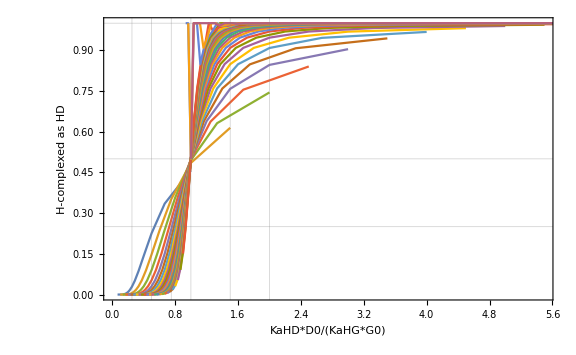

```mathematica
ListLinePlot[th,Frame->True,FrameLabel->{"KaHD*D0/(KaHG*G0)","H-complexed as HD"},ImageSize->Large,GridLines->{{0.25,0.5,0.75,1,1.5,2}, {0.25,0.5,1}}]
```